Note: requires DSDdiagramV1.wl to be loaded.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Surface CRNs: unimolecular (Qian et. al. 2014)

```mathematica
(* assign domain sequences *)
T1="CTCCTC";
T2="ACACAC";
X="CTTCTACTTCATAAC";
RA="CATTTCAACTAAACC";
A="CATCTCATTCTAAAC";
B="CTTACATTTCAACAC";
```

```mathematica
(* assign domain colors *)
cl["T1"]=1;
cl["T2"]=2;
cl["X"]=-1;
cl["RA"]=3;
cl["A"]=5;
cl["B"]=4;
```

```mathematica
(* define strands and complexes *)
gateRAtoB="@90 RA( + ) @90 X*( + B ) @90 T2*";
```

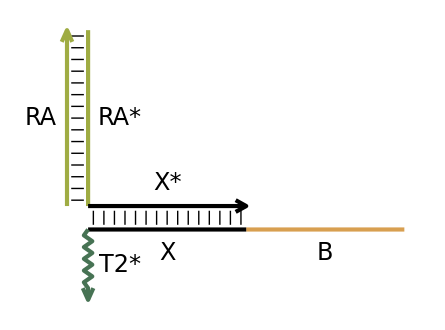

```mathematica
diagramDSD[gateRAtoB,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
```

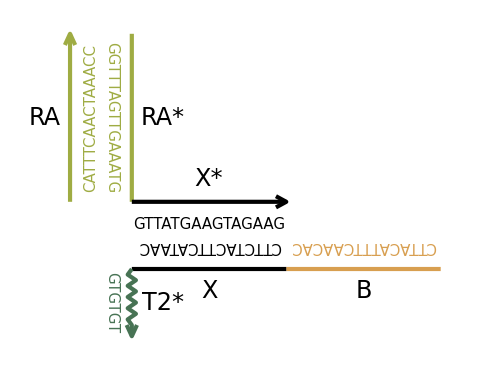

```mathematica
diagramDSD[gateRAtoB,SquiggleToehold->True,DistinctComplement->False,DNASequence->True]
```

### Default style

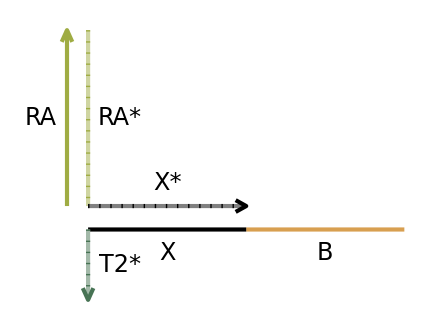

```mathematica
diagramDSD[gateRAtoB]
```

Note: if the dashed lines are not properly displayed on your computer, try using option VectorFormat->False.

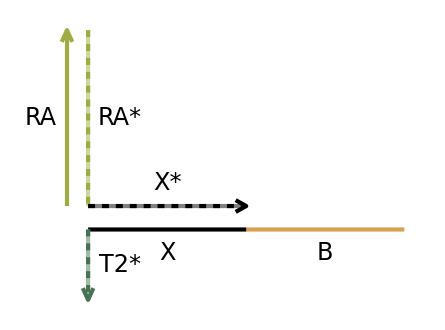

```mathematica
diagramDSD[gateRAtoB,VectorFormat->False]
```

### Alternative style A

```mathematica
(* assign domain colors *)
cl["T1"]=-1;
cl["T2"]=-1;
cl["X"]=-1;
cl["RA"]=-1;
cl["A"]=-1;
cl["B"]=-1;
```

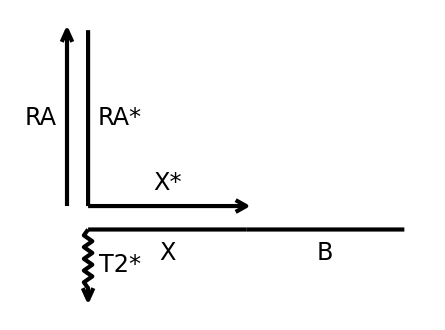

```mathematica
diagramDSD[gateRAtoB,SquiggleToehold->True,DistinctComplement->False]
```

### Alternative style B

```mathematica
(* assign domain colors *)
cl["T1"]=1;
cl["T2"]=2;
cl["X"]=-1;
cl["RA"]=-1;
cl["A"]=-1;
cl["B"]=-1;
```

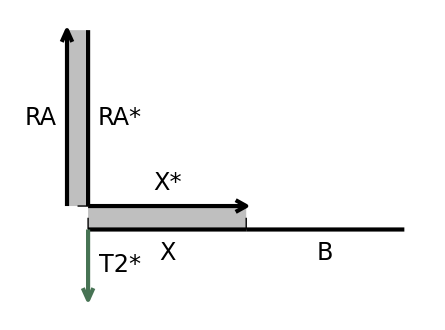

```mathematica
diagramDSD[gateRAtoB,GreyBasepair->True,DomainSeparator->True,DistinctComplement->False]
```

### Alternative style C

```mathematica
(* assign domain colors *)
cl["T1"]=1;
cl["T2"]=2;
cl["X"]=-1;
cl["RA"]=3;
cl["A"]=5;
cl["B"]=4;
```

```mathematica
diagramDSD[gateRAtoB,SquiggleToehold->True,LineBasepair->True,DistinctComplement->False]
```

-Graphics-

### Alternative style D

```mathematica
(* assign domain colors *)
cl["T1"]=1;
cl["T2"]=2;
cl["X"]=-1;
cl["RA"]=3;
cl["A"]=5;
cl["B"]=4;
```

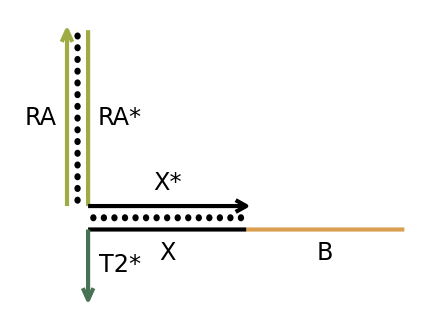

```mathematica
diagramDSD[gateRAtoB,DotBasepair->True,DistinctComplement->False]
```

### Displace sequences

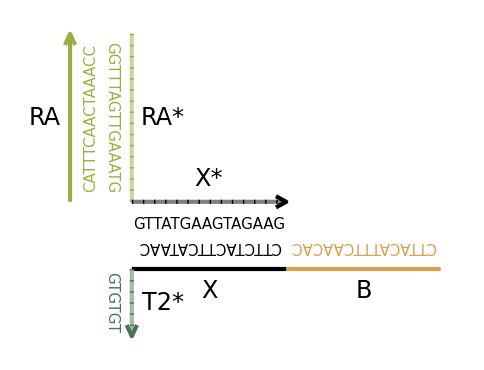

```mathematica
diagramDSD[gateRAtoB,DNASequence->True]
```

### Export diagrams

```mathematica
Export["gateRAtoB.pdf",diagramDSD[gateRAtoB]];
Export["gateRAtoB.svg",diagramDSD[gateRAtoB]];
Export["gateRAtoB.png",diagramDSD[gateRAtoB,VectorFormat->False],ImageResolution->200];
```

```mathematica
Export["gateRAtoB_SEQ.pdf",diagramDSD[gateRAtoB,DNASequence->True]];
Export["gateRAtoB_SEQ.svg",diagramDSD[gateRAtoB,DNASequence->True]];
Export["gateRAtoB_SEQ.png",diagramDSD[gateRAtoB,DNASequence->True,VectorFormat->False],ImageResolution->200];
```

## Hairpin motif (Yin et. al. 2008)

```mathematica
(* assign domain sequences *)
a="GCTTGA";
b="AGGGAG";
c="GTTGTG";
x="GATGTT";
y="TAGTGC";
z="ATTGGA";
```

```mathematica
(* assign domain colors *)
cl["a"]=1;
cl["b"]=3;
cl["c"]=5;
cl["x"]=2;
cl["y"]=4;
cl["z"]=6;
```

```mathematica
(* define strands and complexes *)
strandI="y* b* x* a*";
gateA="a x( b( y( z* c* ) ) )";
gateB="b y( c( z( x* a* ) ) )";
gateC="c z( a( x( y* b* ) ) )";
complexABC="a( x( b( y( z*( c*( y*( b*( x* + ) ) ) ) x*( a*( z*( c*( y* + ) ) ) ) ) ) ) ) z*";
```

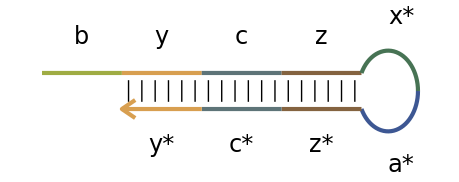

```mathematica
diagramDSD[gateB,DistinctComplement->False,LineBasepair->True]
```

```mathematica
Export["Yin2008gateB.pdf",diagramDSD[gateB,DistinctComplement->False,LineBasepair->True]];
```

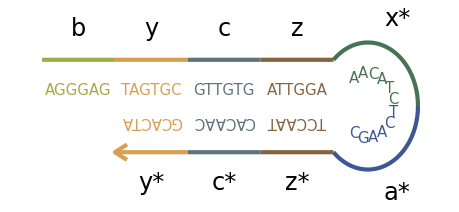

```mathematica
diagramDSD[gateB,DistinctComplement->False,DNASequence->True]
```

```mathematica
Export["Yin2008gateB_SEQ.pdf",diagramDSD[gateB,DistinctComplement->False,DNASequence->True]];
```

### Use AddTurns

Note : AddTurns attempts to calculate the number of branches in a complex and add a turn at each branching point.

```mathematica
AddTurns[complexABC]
```

a( x( b( y( @60 z*( c*( y*( b*( x* + ) ) ) ) @60 x*( a*( z*( c*( y* + ) ) ) ) ) ) ) ) z*

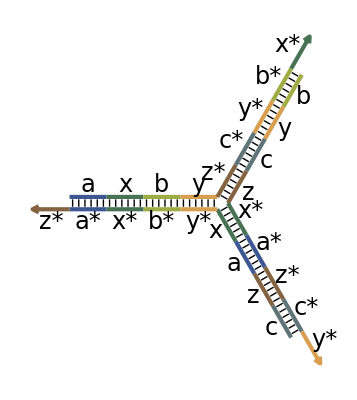

```mathematica
diagramDSD[AddTurns[complexABC],DistinctComplement->False,LineBasepair->True]
```

```mathematica
Export["Yin2008complexABC.pdf",diagramDSD[AddTurns[complexABC],DistinctComplement->False,LineBasepair->True]];
```

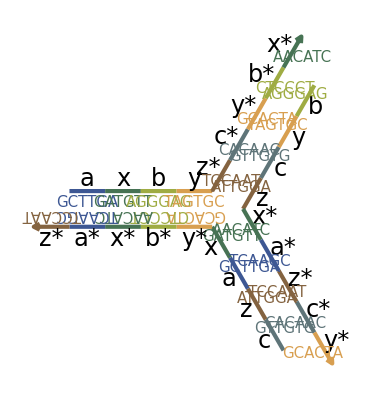

```mathematica
diagramDSD[AddTurns[complexABC],DistinctComplement->False,DNASequence->True]
```

```mathematica
Export["Yin2008complexABC_SEQ.pdf",diagramDSD[AddTurns[complexABC],DistinctComplement->False,DNASequence->True]];
```

## CRNs (Soloveichik et. al. 2010)

```mathematica
(* assign domain sequences *)
S1="NNNNNN";
S2="NNNNNNNNNNNNNNN";
S3="NNNNNN";
S4="NNNNNN";
S5="NNNNNNNNNNNNNNN";
S6="NNNNNN";
S7="NNNNNN";
S8="NNNNNNNNNNNNNNN";
S9="NNNNNN";
S10="NNNNNNNNNNNNNNN";
S11="NNNNNNNNNNNNNNN";
```

```mathematica
(* assign domain colors *)
cl["S1"]=1;
cl["S2"]=-1;
cl["S3"]=1;
cl["S4"]=2;
cl["S5"]=-1;
cl["S6"]=2;
cl["S7"]=3;
cl["S8"]=-1;
cl["S9"]=3;
cl["S10"]=-1;
cl["S11"]=-1;
```

```mathematica
(* define strands and complexes *)
complexT="S10( S4( S5 S6 + S11( S7( S8 S9 + ) ) ) ) S3*";
```

### Use AutoShift

Note: when defining a complex, strands must be listed in an order such that every new strand will be attached to a previously listed strand.  AutoShift attempts to find a strand order that satisfies this requirement.

```mathematica
AutoShift[complexT]
```

S11( S7( S8 S9 + ) ) S4*( S10*( S3* + ) ) S5 S6

```mathematica
(* copy and edit the AutoShift output, e.g. to add turns to the single-stranded domains *)
```

```mathematica
complexT="S11( S7( @60 S8 S9 + ) ) S4*( S10*( S3* + ) ) @60 S5 S6";
```

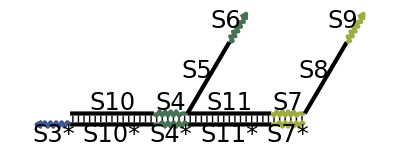

```mathematica
diagramDSD[complexT,SquiggleToehold->True,DistinctComplement->False,LineBasepair->True]
```

### Display nicks

Note : use “:” at the left or right side of a domain to clearly display a nick at the 5’ or 3’ end of the domain.

```mathematica
complexT=":S11( S7( @60 S8 S9 + ) ) S4*( S10*( S3* + ) ) @60 S5 S6";
```

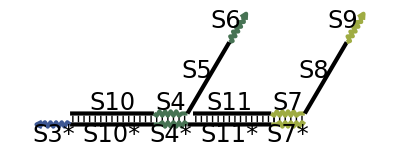

```mathematica
diagramDSD[complexT,SquiggleToehold->True,DistinctComplement->False,LineBasepair->True]
```

```mathematica
Export["Soloveichik2010complexT.pdf",diagramDSD[complexT,SquiggleToehold->True,DistinctComplement->False,LineBasepair->True]];
```

## Seesaw motif (Qian et. al. 2011)

```mathematica
(* assign domain sequences *)
T="TCTAC";
S5="CACCACCAAACTTCA";
S6="CATAACACAATCACA";
```

```mathematica
(* assign domain colors *)
cl["T"]=1;
cl["S5"]=4;
cl["S6"]=3;
```

```mathematica
(* define strands and complexes *)
Gate56="S5( T( @60 S6 + ) ) T*";
```

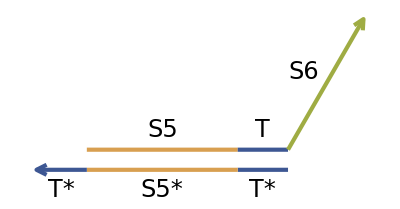

```mathematica
diagramDSD[Gate56,DistinctComplement->False]
```

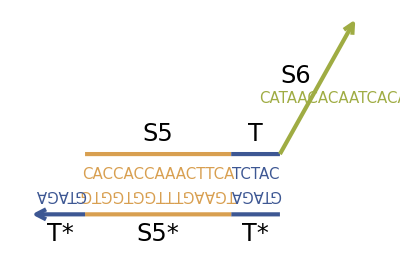

```mathematica
diagramDSD[Gate56,DistinctComplement->False,DNASequence->True]
```

### Reverse the strand orientation

Note : the default strand orientation is from 5’ to 3’. Use “ReverseOrient→True” to reverse the strand orientation.

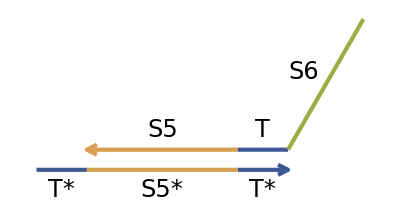

```mathematica
diagramDSD[Gate56,DistinctComplement->False,ReverseOrient->True]
```

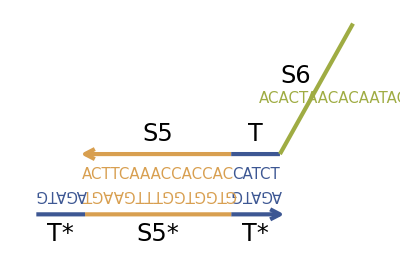

```mathematica
diagramDSD[Gate56,DistinctComplement->False,ReverseOrient->True,DNASequence->True]
```

```mathematica
Export["SeesawGate56.pdf",diagramDSD[Gate56,DistinctComplement->False,ReverseOrient->True]];
```

### Change the font size of domain labels

Note : the default font size of domain labels is 24. Use “DomainLabelSize→FontSize” to make the labels larger or smaller.

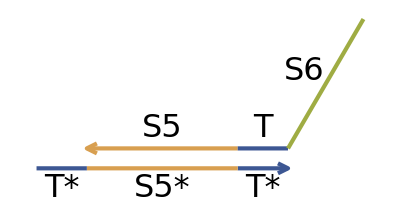

```mathematica
diagramDSD[Gate56,DistinctComplement->False,ReverseOrient->True,DomainLabelSize->32]
```

```mathematica
Export["SeesawGate56.pdf",diagramDSD[Gate56,DistinctComplement->False,ReverseOrient->True]];
```

### Add fluorophores and quenchers

Note : fluorophores and quenchers are treated as special domains with a “_” in front of the names.

```mathematica
(* assign fluorophore and quencher labels *)
F="ROX";
Q="RQ";
```

```mathematica
(* assign fluorophore and quencher colors *)
cl["F"]=RGBColor[0.7,0,0];
cl["Q"]=Black;
```

```mathematica
(* define strands and complexes *)
Rep6="S6( _Q + _F ) T*";
```

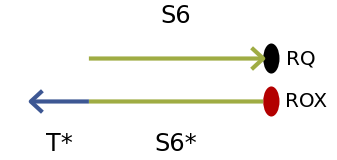

```mathematica
diagramDSD[Rep6,DistinctComplement->False]
```

```mathematica
Export["SeesawRep6.pdf",diagramDSD[Rep6,DistinctComplement->False]];
```